```mathematica
BeginPackage["MeFuncs`"];

xH={1,0};
yH={0,1};
rH={Cos[#],Sin[#]}&;

$PrePrint=StandardForm;
(*Begin["`Private`"]*)
CsQ:=DeleteElements[#[[1]]*#[[2]],{0}]&[{#,Flatten[Attributes[#]/.{Constant->1,{}->{0}}]}]&[Vars[#]]&
Flatn:=DeleteElements[#[[2]],#[[1]]]&[Flatten/@{{List@@({##}/.#1->{Null})},#1}]&
FNCheck:=Module[{},Print[{#1,#2,#3}];Print[Defer[#2[#1]==#3[#1]]];#2[#1]==#3[#1]]&
Intg:=Extract[#,Flatn[{Position[#,Integrate]},0]][[1]]&[FullForm[#]]&
Intl:=Extract[#,Flatn[{Position[#,Integrate]},0]][[2]]&[FullForm[#]]&
Mag:=If[VectorQ[#],Sqrt[#.#],#]&;
RP:=If[ContainsAny[{0,Null},##],#[[2]],#[[2]]//.Thread[#[[3]]->#[[4]]],MaxIterations->5]&[{(Times@@Flatten[{##}/.Thread[{#1,#2,#3}->{1,1,1}]]),#1,#2,#3}]&
RPT:=Express_:>Module[{},
(Express/.If[!ContainsAny[{0,Null,{}},{##}],Thread[#2->#3],Thread[#3->#3]])&[Times@@Flatten[{##}/.{#1->1,#2->1}],#1,#2]
]&
SS:=#[[1]]/.Solve[#[[2]]==0,#[[1]]][[If[#[[3]]===Null,1,#[[3]]]]]&[{#1,#2,Times@@({##}/.Thread[{#1,#2}->{1,1}])}]&
S:=If[#2===3,#1/.g21[],#1]&[If[AnyMatch[{2,3},#2],TrigReduce[#1],#1],#2]&[If[AnyMatch[{0,Null},#2],#1,
Refine[FullSimplify[#1],Variables[#1]∈Reals]/.Abs[q_]:>q],#2]&[#1,(Times@@({##}/.#1->1))]&;

g20:=Express_:>Module[{},
Express/.Thread[#2[[2]]*#2[[1]]->ConstantArray[0,Length[#2[[1]]]]]&[Express,##]&[If[##===Null,
{{},1},
If[ContainsAny[{Null},{##}],
{{##}[[1]],0},
{{##}[[1]],1}]]]]&
g21:=Express_:>Module[{},
Express/.Thread[#2[[2]]*Join[#2[[1]],#3[[1]]]->#2[[2]]*ConstantArray[1,Length[Join[#2[[1]],#3[[1]]]]]]&[##,{DeleteCases[(Boole[MemberQ[Attributes[#],Constant]&/@Vars[#1]])*(#&/@Vars[#1]),0],Vars[#1]}]&[Express,##]&[If[##===Null,
{{},1},
If[ContainsAny[{Null},{##}],
{{##}[[1]],0},
{{##}[[1]],1}]]]]&

Trm:=If[Head[Expand[#]]===Plus,List@@Expand[#],{#}]&;
Vars:=If[AnyMatch[{0,Null},#2],(DeleteCases[Dt/@#1,0]/.HoldPattern[Dt[q_]]:>q),#1]&[Variables[#1//.{f_[q_]|Exp[q_]:>q}],#2]&[(If[Head[Trm[#1][[1]]]===Power,(Trm[#1][[1,1]]),Trm[#1]]),(Times@@Flatten[{##}/.#1->1])]&
(*!FreeQ[#,Integrate]*)
QA:=Table[#1,{#2,#3}]&[#1,If[AnyMatch[{1,Null},#1],i,Vars[#1][[1]]],#2]&;

d:=Nest[Dt,#1,Times@@(##/#1)]//.HoldPattern[Dt[q_Symbol]]->Derivative[1][q]&
Format[Derivative[n_][f_]]=OverDot[f,n];

PRM[param_:t,unParam_:0]:=Express_:>Module[{Terms,vars,args,maps},
Catch[
Terms=If[Head[Expand[#]]===Plus,List@@Expand[#],{#}]&[Express/.g21[]];
vars=Variables[Terms];
If[!unParam==0,Throw[Express//.(OverDot[q_,n_]->Derivative[n][q]&)/@vars;Express//.(q_[param]->q&)/@vars]];
args=Vars[vars];
maps=Table[If[!MatchQ[vars[[i]],Derivative[n_][f_][param]|Derivative[n_][f_]],
vars[[i]]/.(#->#[param]&)/@args,
If[MatchQ[vars[[i]],Derivative[n_][f_]],
vars[[i]]/.Derivative[n_][f_]->Derivative[n][f][param],
vars[[i]]
]
],
{i,Length[vars]}];
Express/.Thread[vars->maps]
]
];

(*End[]*)
EndPackage[]
```

```mathematica
Quit
```

```mathematica
ClearAll["Global`*"]
SysVars={{t,t0,tf,m,u},{r,a}}(*{h,R,M,M2,m,g};*)
SetAttributes[{t,t0,tf,m,u},Constant]
$Assumptions=And@@(#>0&&Element[#,Reals]&/@Flatten[SysVars])
```

{{t,t0,tf,m,u},{r,a}}

t>0&&t∈ℝ&&t0>0&&t0∈ℝ&&tf>0&&tf∈ℝ&&m>0&&m∈ℝ&&u>0&&u∈ℝ&&r>0&&r∈ℝ&&a>0&&a∈ℝ

```mathematica
C2P@{x,y,0}/.r->m
d[C2P@{x,y}/.r->m]
Cross[{m Cos[a],m Sin[a],-z0},g*{-m Sin[a] ȧ,m Cos[a] ȧ,0}]/.RPT[{a},{p}]
```

{m Cos[a],m Sin[a],0}

{-m Sin[a] ȧ,m Cos[a] ȧ}

{g m z0 Cos[p] ṗ,g m z0 ṗ Sin[p],g m^2 Cos[p]^2 ṗ+g m^2 ṗ Sin[p]^2}

```mathematica
Mag[{Cos[a]/Sin[a],0,1}]
```

√(1+Cot[a]^2)

```mathematica
Simplify[√(1+Cot[a]^2)]
```

Abs[Csc[a]]

```mathematica
SetAttributes[IntTricks,HoldAll];
(*Calling IntTricks[[2,2,2,2,1]] gives the first replacement rule*)
IntTricks=Integrate[expr_,{t,t0_,tf_}]:>
Module[{Terms,Tricks,Integrals,FnDecoder,InverseSubs,Result},
Terms=If[Head[Expand[expr]]===Plus,List@@Expand[expr],{expr}];

Tricks={(*Order matters here. Terms will go to first match => Complex to simple listing chosen*)
c_.*f_[c2_.*q_[t]]*q_'[t]:>c*Integrate[f[c2*q],{q,q[t0],q[tf]}],
c_.*f1_[c1_.*q_[t]]*f2_[c2_.*q_[t]]*q_'[t]:>c*Integrate[f1[c1*q]*f2[c2*q],{q,q[t0],q[tf]}],
c_.*q_'[t]:>c*Integrate[1,{q,q[t0],q[tf]}],

c_.*f_[c2_.*q_]*q_':>c*Integrate[f[c2*q],{q,q[t0],q[tf]}],
c_.*f1_[c1_.*q_]*f2_[c2_.*q_]*q_':>c*Integrate[f1[c1*q]*f2[c2*q],{q,q[t0],q[tf]}],
c_.*q_':>c*Integrate[1,{q,q[t0],q[tf]}],
(*f1_[c1_.*q1_[t]]*f2_[c2_.*q2_[t]]*q2_'[t]*q3_[t]:>f1[c1*q1[t]]*q3[t]*Integrate[f2[c2*q2],{q2,q2[t0],q2[tf]}],*)
(*f1_[c1_.*q1_[t]]*f2_[c2_.*q2_[t]]*q2_'[t]:>f1[c1*q1[t]]*Integrate[f2[c2*q2],{q2,q2[t0],q2[tf]}],*)
(*f1_[c1_.t]*f2_[c2_.*q_[t]]*q_'[t]:>f1[c1*t]*Integrate[f2[c2*q],{q,q[t0],q[tf]}],*)
(*f_[c1_.*q_[t]]*q_'[t]:>Integrate[f[c1*q],{q,q[t0],q[tf]}],*)
(*f_[c1_.*q1_[t]]*q2_'[t]:>f[c1*q1[t]]*Integrate[1,{q2,q2[t0],q2[tf]}],*)
(*f1_[c1_.*q1_[t]]*f2_[c2_.*q2_[t]]*q2_'[t]:>f1[c1*q1[t]]*Integrate[f2[c2*q2],{q2,q2[t0],q2[tf]}],
f_[t]:>Integrate[f[t],{t,t0,tf}],*)

c_.*q_[t]*q_'[t]:>c*Integrate[q,{q,q[t0],q[tf]}],
c_.*q_'[t]:>c*Integrate[1,{q,q[t0],q[tf]}],

c_.*q_*q_':>c*Integrate[q,{q,q[t0],q[tf]}],
c_.*q_':>c*Integrate[1,{q,q[t0],q[tf]}]
(*q1_[t]*q2_[t]*q1_'[t]:>q2[t]*Integrate[q1[t],{q1,q1[0],q1[f]}],
q_[t]*q_'[t]:>Integrate[q[t],{q,q[0],q[f]}],
(q1_[t])^c1_.*q2_'[t]:>(q1[t])^c1*Integrate[1,{q2,q2[0],q2[f]}],
q_'[t]:>Integrate[1,{q,q[0],q[f]}]*)
};

	Integrals=Terms/.Tricks;
Result=Plus@@Integrals/.{t0->0,tf->t}(*/.InverseSubs*)
];/;FreeQ[expr,Integrate];

V2D[Integrand_]:=-Integrate[Integrand,{t,t0,tf}];

ELeq[T_,V_,qs_,Cons_,ShowBool_:0]:=
Module[{L,λs,ELUnCons,ConsQ,ELCons,EqnsUnCon,EqnsCon,Show},
		L=T-V;
	
	ELUnCons[Lag_,var_]:=(d[D[Lag,d[var]]]-D[Lag,var])/.(0&)->0;
	EqnsUnCon=Table[ELUnCons[L,qs[[i]]],{i,Length[qs]}];
If[Length[Cons]==0,
EqnsCon={};,

	λs=Symbol/@("λ"<>ToString[#]&/@Range[Length[Cons]]);
ELCons[UnkMult_,Constraint_,var_]:=(UnkMult*D[Constraint,var])/.(0&)->0;
EqnsCon=Table[ELCons[λs[[i]],Cons[[i]],qs[[j]]],{i,1,Length[Cons]},{j,1,Length[qs]}];
];

Show=If[ShowBool==1,
Print[L];
Print[TableForm[EqnsUnCon-Total[EqnsCon],
TableHeadings->{qs,None},TableSpacing->{1,5}]];
If[Length[Cons]>0,
Print[TableForm[Flatten[EqnsCon],
TableHeadings->{Tuples[{λs,qs}],None},TableSpacing->{1,5}]];
]
];
Return[Join[EqnsUnCon-Total[EqnsCon],EqnsCon]]
]
```

```mathematica
C2P=RP[#,{x,y},{(r*Cos[a]),(r*Sin[a])},1]&; (*Use like C2P@{x,y}*)
P2C=RP[#,{Cos[a],Cos[p],Sin[a],Sin[p]},{Sqrt[x^2+y^2],x/Sqrt[x^2+y^2],y/Sqrt[x^2+y^2]}]&;
```

```mathematica
TC[x_,y_]=m/2(d[x]^2+d[y]^2)
TP[r_,a_]=m/2(d[r*Cos[a]]^2+d[(r*Sin[a])]^2)

(*	Ipill[r]=RP[Integrate[(M2/r)r'^2,{r',0,r}],{r,M2},{2*h/3,2/3*M}];
TP[a_]=1/2Ipill[r]*d[a]^2;TP[t_]=TP[a]/.PRM[]*)
```

1/2 m ((ẋ)^2+(ẏ)^2)

1/2 m ((-r Sin[a] ȧ+Cos[a] ṙ)^2+(r Cos[a] ȧ+Sin[a] ṙ)^2)

```mathematica
FullForm[TC[r,a]]
```

Times[Rational[1,2],m,Plus[Power[Derivative[1][a],2],Power[Derivative[1][r],2]]]

```mathematica
Tg[a_]=S[C2P@Cross[{x,y,0},m*g{0,-Sin[π/2-a],0}]]
```

```mathematica
(*Fg[a_]=RP[M2*g*Cos[a]{Sin[a],-Cos[a]},{r,M2},{2*h/3,2/3*M}](*FN[a_]=m*g*Sin[a]*{Cos[a],Sin[a]};*)(*F[a_]=Fg+FN[a]*)*)
Fg=m*g{0,1};FN[p_]=-m*g*{Sin[p],Cos[p]};
Fg+FN[p];
ParametricPlot[{FN[p]+Fg/.g21[]},{p,2π,0},AxesLabel->{"x","y"},AspectRatio->1];
```

```mathematica
TestV[a_]=Integrate[Fg[ap],{ap,π/2,a}];
TestP[a_]=Integrate[TestV[ap],{ap,π/2,a}];
```

```mathematica
Plot[{Fg[a]/.g21[],TestP[a]/.g21[]},{a,π/2,0},ScalingFunctions->{"Reverse",Identity}];
ParametricPlot[{{Fg[a]/.g21[]},{TestP[a]/.g21[]}},{a,π/2,0},AxesLabel->{"x","y"},AspectRatio->1];
```

```mathematica
lC[x_,y_]:={x,y}; lP[r_,a_]:={r*Cos[a],r*Sin[a]};
dlC[x_,y_]:=d[lC[x,y]];dlP[r_,a_]:=RP[d[lP[r,a]],{},{}];
dlC[x,y];
dlP[r,a];
(*Vintgs={S[((Fg+FN[p])).dlC[x,y]]/.RPT[{x',y'},{R(Sin[a[t]])}]/.PRM[t],S[(Fg+FN[p]).dlP[r,a],0]/.PRM[t]}*)
Vintgs={u/(x^2+y^2),u/r^2}
VCint[x_,y_]=Vintgs[[1]];VPint[r_,a_]=Vintgs[[2]];
```

{u/(x^2+y^2),u/r^2}

```mathematica
Vs=RP[{V2D[VCint[x,y]]/.IntTricks,V2D[VPint[r,a]]/.IntTricks},{},{}];
Vs={u/(x^2+y^2),u/r^2}
VC[x_,y_]=Vs[[1]];VP[r_,a_]=Vs[[2]];
```

{u/(x^2+y^2),u/r^2}

```mathematica
(*LC[t_]:=RP[TC[t]-VC[t],{r[t],r'[t]},{R,0},0];*)
(*LP[t_]:=RP[TP[t]-(α/r^2/.PRM[t]),{r[t],r'[t]},{R,0},0];*)
LC[x_,y_]:=RP[TC[x,y]-VC[x,y],{r,r'},{R,0},0];LC[x,y]
LP[r_,a_]:=RP[TP[r,a]-VP[r,a],{r,r'},{R,0},0];LP[r,a]
```

-u/(x^2+y^2)+1/2 m ((ẋ)^2+(ẏ)^2)

-u/r^2+1/2 m ((-r Sin[a] ȧ+Cos[a] ṙ)^2+(r Cos[a] ȧ+Sin[a] ṙ)^2)

```mathematica
Conx[t_]:=0;(*x[t]^2+y[t]^2-R^2/.RPT[{R},{(2h/3)}]*)
Cony[t_]:=0;(*x[t]^2+y[t]^2-R^2/.RPT[{R},{(2h/3)}]*)
ELegsC[t_]=ELeq[TC[x,y],VC[x,y],{x,y},{},1];
```

-u/(x^2+y^2)+1/2 m ((ẋ)^2+(ẏ)^2)

x | -(2 u x)/((x^2+y^2)^2)+m ẍ
y | -(2 u y)/((x^2+y^2)^2)+m ÿ

```mathematica
Conr[t_]:=0;(*r[t]-R/.RPT[{R},{2h/3}];*)
(*Cona[t_]=S[Mag[Fg*Sin[a[t]]-(FN[a]/.PRM[])]-m*r[t]*a'[t]^2]*)
Cona[t_]:=0;(*Fg[t].xH*)
ELegsP[t_]=ELeq[S[TP[r,a]],S[VP[r,a]],{r,a},{},1];
```

-u/r^2+1/2 m (r^2 (ȧ)^2+(ṙ)^2)

r | -(2 u)/r^3-m r (ȧ)^2+m r̈
a | 2 m r ȧ ṙ+m r^2 ä

```mathematica
ErT[t_]=ELeq[S[TP[r,a]],S[VP[r,a]],{r,a},{}][[1]]/.RPT[{λ1,λ2},{0,0}];
EaT[t_]=ELeq[S[TP[r,a]],S[VP[r,a]],{r,a},{}][[2]]/.RPT[{λ1,λ2},{0,0}];
EPtotT[t_]=S[ErT[t]+EaT[t],0];
```

```mathematica
EPs=RP[{{S[ErT[t]]},{S[EaT[t]]},{S[EPtotT[t]]}},{r[t],r[0]},{2h/3,2h/3},0]
Er=EPs[[1,1]];Ea=EPs[[2,1]];EPtot=EPs[[3,1]];

EPCs={{#[[3,1]],#[[3,2]]},{#[[4,1]],#[[4,2]]}}&[S[RP[ELeq[TP[r,a],VP[r,a],{r,a},{Conr[t],Cona[t]}],{λ1,λ2},{0,0},1],1]]/.PRM[t,1];
```

{{-(2 u)/r^3-m r (ȧ)^2+m r̈},{m r (2 ȧ ṙ+r ä)},{-(2 u)/r^3+m (r (-(ȧ)^2+2 ȧ ṙ+r ä)+r̈)}}

```mathematica
Er/.RPT[{m*r*a'^2},{v}]
```

-(2 u)/r^3-v+m r̈

0

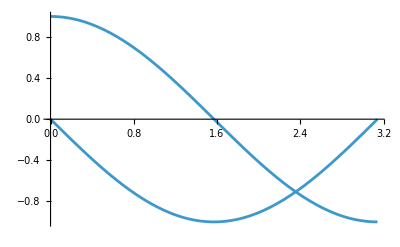

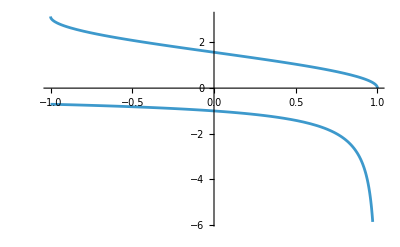

```mathematica
x1[a1_]=r1*Cos[a1];
a1[x1_]=ArcCos[x1/r1];
dx1[a1_]=-r1*Sin[a1];
da1[x1_]=-1/Sqrt[1-x1/r1^2];
D[a1,x1]
Plot[{x1[a1],dx1[a1]}/.r1->1,{a1,0,π}]
Plot[{a1[x1],da1[x1]}/.r1->1,{x1,1,-1}]
```

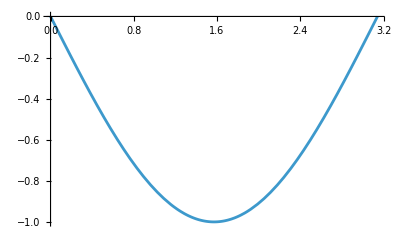

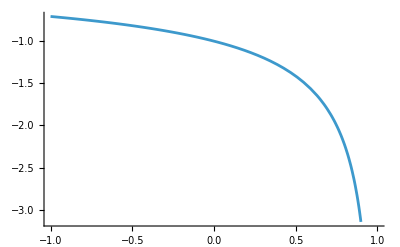

```mathematica
Plot[dx1[a1]/.r1->1,{a1,0,π}]
Plot[da1[x1]/.r1->1,{x1,1,-1}]
```

```mathematica
-m r (ȧ)^2+2m r ȧ ṙ+m r^2 ä+OverDoubleDot[mr]
```

```mathematica
d[1/r^3]
```

```mathematica
-D[2*u/r^3,r]
```

```mathematica
(-2u/r^3-L^2/m*r+m*r'')
(-2u/r^3-m*r*a'^2+6u/r^4)
```

```mathematica
2 m r ȧ ṙ+2 a m (ṙ)^2+2 a m r r̈
```

```mathematica
-m r (ȧ)^2+OverDoubleDot[mr]
```

At some point, with α=0, the particle makes it to a position r=b. At this point the force on the particle should be maximized, with a’’=0 since they’re only radial at this point. When r=b

```mathematica
SS[a',Er]
RP[Ea,{a'},{SS[a',Er]}]
RP[Ea,{a',α,r,r',r''},{SS[a',Er],0,b,r',r''},];
```

```mathematica
SS[a'',Ea]
```

```mathematica
Integrate[SS[a'',Ea],{a,a[0],af}]
```

```mathematica
ErSols=SS[a',EPs0[[1,1]]]
EaSols=RP[S[SS[a'',EPs0[[2,1]]]],{r,r[0]},{2h/3,2h/3}]
```

```mathematica
RP[S[RP[Ea,{a'},{ErSols[[1]]}]],{r',r''},{0,0}]
SS[a'',%]
```

```mathematica
EPs=RP[RP[{{S[ErT[t]/.PRM[t,1]]},{S[EaT[t]/.PRM[t,1]]},{S[EPtotT[t]/.PRM[t,1]]}},{a''},{-(g/r)*Cos[a]}],{r',r''},{0,0}]
Er=EPs[[1,1]];Ea=EPs[[2,1]];EPtot=EPs[[3,1]];
```

```mathematica
SS[a',Er]
```

```mathematica
S[RP[Cona[t]/.PRM[t,1],{a'},{SS[a',Er]}]]
SS[a[0],%]
```

```mathematica
Plot[ArcSin[Sin[a]-√2 Sin[a] √(1+Sin[a])],{a,- π, π}]
```